# Hyperfine Simulation

```mathematica
(* Some Constants *)
m = 9.10938356 10^(-31) (* Electron mass, kg *);
h = 6.62607015 10^(-34);
hbar = h/(2 π);
c = 299792458;
q = 1.60217662 10^(-19);
ϵ = 8.85418782 10^(-12);
e = Sqrt[q^2/(4 π ϵ)];
a = hbar^2/(m e^2); (* Bohr Radius *)
f[n1_, n2_] := ( m q^4)/(8 h^3 ϵ^2) (1/(n1^2) - 1/(n2^2));
k = 1.380649 10^-23; (* Boltzmann Constant *)
mh = 1.6735575 10^-27; (* Hydrogen Mass, kg *)
μ0 = 10^-7 4 π;
```

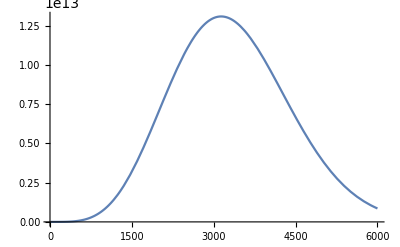

```mathematica
(* Modified Maxwellian Velocity Distribution *)
temp =298;
areavel[mina_,maxa_] := NIntegrate[x^4 Exp[-x^2 (mh/(2k temp))], {x,mina,maxa}];
F[y_] :=y^4 Exp[-y^2 (mh/(2k temp))];
Plot[ F[y], {y, 10,6000},PlotRange->All] 
Integrate[F[y], {y,400,405}];
maxvel = Flatten[Solve[F'[y] == 0,y]];
maxvel[[5,2]];
```

```mathematica
f[x_] := 0.5 Exp[-(x-0.04)^2/0.015^2]
Plot[Mag[t,0.01,0,100], {t,0,32},PlotRange->All];
```

```mathematica
Plot[Magform[0.5,z], {z,-0.05,0.05},PlotRange->All];
```

```mathematica
Magform[0.5,z];
```

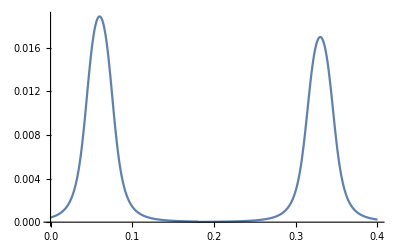

```mathematica
(* Define parameters for experiment (phase, magnetic fields, etc. )*)
ϕ=-0.012;
deadlength = 0.26;
totallength = 2 coillength+deadlength;
VPulse = 70;
B2[mV_] := mV(Pi/2)/VPulse 10000 h maxvel[[5,2]]/(2Pi 0.03 gj μb β);
B2[30];

(* Field expressions for circular finite length solenoid *)
r0 = 0.015;
coillength = 0.03;
m1[r_,z_] := 4 r0 r /((r0 +r)^2+(z+coillength/2)^2);
m2[r_,z_] := 4 r0 r/((r0+r)^2+(z-coillength/2)^2);
u[r_] := 4 r0 r/(r0+r)^2;
Bz[mV_,z_, r_] :=B2[mV](z+coillength/2)/(4Pi)Sqrt[m1[r,z]/(r0 r)](EllipticK[m1[r,z]]+(r0-r)/(r0+r) EllipticPi[u[r],m1[r,z]])-B2[mV](z-coillength/2)/(4Pi)Sqrt[m2[r,z]/(r0 r)](EllipticK[m2[r,z]]+(r0-r)/(r0+r) EllipticPi[u[r],m2[r,z]]);
Magform[mV_,z_]:=Limit[Bz[mV,z,r], r-> 0];

η = 377;
A =2Pi 0.015^2;
amps = 0.05/55;

ω0 = 2Pi 177.5568 10^6;
ω1 = 2 Pi 1087 10^6;
ω2 = 2Pi 909 10^6;
Mat2S2P = 1.94367 10^-8;

El[λ_, r_,I_,θ_,area_] :=  η (2Pi/λ)^2 (I area) Sin[θ] (1+ 1/((2Pi/λ) r))Exp[-ⅈ (2Pi/λ)r]/(100 4Pi r);

Echange00[λ_,ω_,r_] :=0.5(Mat2S2P)^2 q^2 (El[λ,r,amps, 90 Degree,A])^2 ((1/9)/(hbar ω1- hbar ω)+(1/9)/(hbar ω1+hbar ω));
Echange10[λ_,ω_,r_] := 0.5(Mat2S2P)^2 q^2 (El[λ,r,amps, 90 Degree,A])^2((1/9)/((hbar ω2)-hbar ω)+(1/9)/((hbar ω2)+hbar ω));
ChangeHyperfine[λ_, ω_,r_] := (Echange00[λ, ω,r]-Echange10[λ, ω,r])/h;
Plot[ChangeHyperfine[0.3, 908 10^6 2Pi, r -0.38],{r,0, 0.34}, PlotRange->All];

Mag[t_,v_,ϕ_,mV_] := Piecewise[
{{Magform[mV, v t-0.06] Exp[ⅈ ϕ] ,0.15+coillength>=v t>=0},
{0,deadlength+coillength-0.15>=v t>=coillength+0.07},
{0.9 Magform[mV, v t-(deadlength+coillength+0.04)] ,totallength+0.09>=v t>=deadlength+coillength-0.15},
{0,v t>=totallength+0.04}}];
Plot[Mag[t,1,0,100],{t,0,0.4},PlotRange->All]

Mag2[t_,v_,ϕ_,B_] := Piecewise[{{0,v t<=0},{B Exp[ⅈ ϕ] ,coillength>=v t>=0},{0,deadlength+coillength>=v t>=coillength},{B ,totallength>=v t>=deadlength+coillength},{0,v t>=totallength}}];

β = 1/2; 
μb = 9.274 10^-24;
gj = 2;
Ω[t_,v_,ϕ_,mV_]:= 2Pi gj μb β Mag[t,v,ϕ,mV]/10000/(h); 
γ = 1.3 2 Pi;
δ[Δ_,Bsol_,v_,t_,mV_] := (Δ) 10^3 - 2Pi 22.184 10^3 Bsol^2+2Pi 0.007 mV^2;
σ1[Bsol_] :=- 2Pi 22.184 10^3 Bsol^2 ;
σ2[Bsol_] :=2Pi 1.4 10^6 Bsol;
Ωx1[t_,v_,ϕ_,B_] := 2Pi(Mag2[ t, v,ϕ,B]/10000) μb /(2Sqrt[2]h);
Ωx2[t_,v_,ϕ_,B_] := 0;
Ωy1[t_,v_,ϕ_,B_] := 2Pi(Mag2[t, v,ϕ,B]/10000) μb /(2Sqrt[2]h);
Ωy2[t_,v_,ϕ_,B_] := 0;

min = -12Pi/2;
max = 12 Pi/2;
delta = 0.5;
velmin =100; (* Minimum velocity of hydrogen atoms *)
velmax =6000; (* Maximum velocity of hydrogen atoms *)
deltav =100;
normfact = Sum[F[velmin+deltav i],{i,0,(velmax-velmin)/deltav,1}]; 
Bx =0 10^-3;
By =0 10^-3;
Bsolmin = -0.02;
Bsolmax = 0.02;
deltaBsol = 0.003;
Bsoltest = 20 10^-3;
mVmin = 10;
mVmax=30;
mVdelta = 10;
phimin = -0.05;
phimax = 0.05;
phidelta = 0.05;
```

```mathematica
70^2 0.007
```

34.3

```mathematica
0.007 30^2
```

6.3

```mathematica
Magform[1,z];
```

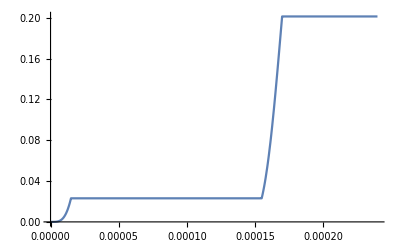

```mathematica
vtest = 2000;
B2 = 0.002300;
D2 = NDSolve[{
c1'[t] == - ⅈ (σ2[0.00]c1[t]+Ωx[Bx3,t,vtest]c3[t]),
c2'[t] == - ⅈ (σ2[0.00]c2[t]+Ωx[Bx3,t,vtest] c3[t]),
c3'[t]==- ⅈ (Ωx[Bx3,t,vtest](c1[t]+c2[t])+(Ω[B2,t,vtest]/2) c4[t]),
c4'[t]==- ⅈ (Ω[B2,t,vtest]/2c3[t]- 0 10^3 c4[t]),
c1[0] == 0, c2[0] == 0,c3[0] ==0, c4[0] ==1}, {c1,c2,c3,c4}, {t,0,1.2 0.4/vtest}]; 
c1a[t_] = c1[t] /. D2[[1]];
c2a[t_] = c2[t] /. D2[[1]];
c3a[t_] = c3[t] /. D2[[1]];
c4a[t_] = c4[t] /. D2[[1]];
Abs[c1a[1.2 0.4/vtest]]^2;
Plot[Abs[c1a[t]]^2, {t,0,1.2 0.4/vtest}, PlotRange->All]
```

```mathematica
Diffsolve = 
ParallelTable[
Diffs = NDSolve[{
c1'[t] == - ⅈ (σ2[Bsoltest]c1[t] +(Ωx1[t,v,ϕ1,Bx]-ⅈ Ωy1[t,v,ϕ1,By])c3[t]),
c2'[t] == - ⅈ (-σ2[Bsoltest]c2[t]+(Ωx2[t,v,ϕ1,Bx]+ⅈ Ωy2[t,v,ϕ1,By]) c3[t]),
c3'[t]==- ⅈ (Ωx1[t,v,ϕ1,Bx]c1[t]+Ωx2[t,v,ϕ1,Bx]c2[t]+ⅈ Ωy1[t,v,ϕ1,By]c1[t]-ⅈ Ωy2[t,v,ϕ1,By]c2[t]+(Ω[t,v,ϕ1,100]/2 ) c4[t]),
c4'[t]==- ⅈ ((Ω[t,v,ϕ1,100]/2 )c3[t]-δ[Δ,Bsoltest,v,t,100] c4[t]),
c1[0] ==0, c2[0]==0,c3[0] == 0, c4[0]==1}, {c1,c2,c3,c4}, {t,0,0.48/v}]; 
c1a[t_] = c1[t] /.Diffs[[1]];
c2a[t_] = c2[t] /. Diffs[[1]];
c3a[t_] = c3[t] /. Diffs[[1]];
c4a[t_] = c4[t] /. Diffs[[1]];
Abs[c3a[1.2 0.4/v]]^2+Abs[c1a[1.2 0.4/v]]^2+Abs[c2a[1.2 0.4/v]]^2,{ϕ1, phimin,phimax,phidelta},{v, velmin, velmax, deltav},{Δ, min,max,delta}];
weighted = ParallelTable[F[velmin+deltav i-deltav]Diffsolve[[j,i]],{j,1,Length[Diffsolve],1},{i,1,Length[Diffsolve[[1]]],1}];
meanweighted =ParallelTable[Sum[weighted[[i,j]],{j, 1, Length[weighted[[1]]]}], {i, 1, Length[weighted]}]/normfact;
plotvar = Table[i/(2 Pi), {i,min,max,delta}];
finaldata=Table[{plotvar[[j]],meanweighted[[i,j]]}, {i,1,Length[Diffsolve],1}, {j,1, Length[meanweighted[[1]]]}];
```

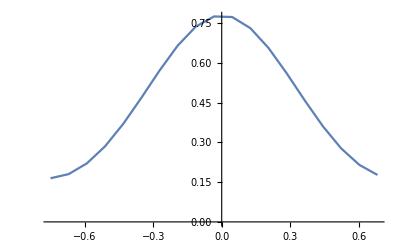

```mathematica
ListLinePlot[finaldata[[2]], PlotRange->All]
```

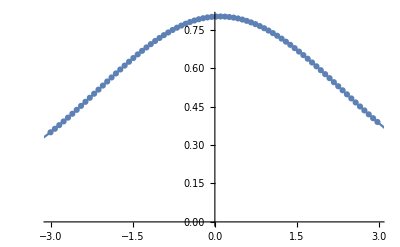

4676.91

96.4072

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
offset | 0.169267 | 0.000782136 | 216.416 | 4.6898×10^-103
Amp | 0.632751 | 0.000754461 | 838.679 | 2.16393×10^-145
Γ | 1.7069 | 0.00151888 | 1123.79 | 1.53302×10^-154
x1 | 0.0964072 | 0.000192308 | 501.316 | 2.65015×10^-129

```mathematica
num =3;
fitfunc[x_] := offset + Amp Sinc[(x-x1)/Γ]^2;
fitfunc2[x_] := offset + Amp Exp[((x-x1)/Γ)^2];
mf =NonlinearModelFit[finaldata[[num]], {fitfunc[x],Γ>0},{ {offset,0.05}, {Amp,0.3},{Γ,0.55},{x1,0.01}}, x];
Show[ListPlot[finaldata[[num]]],Plot[mf[[1,2,1,2]]+mf[[1,2,2,2]]Sinc[ (x-mf[[1,2,4,2]])/mf[[1,2,3,2]]]^2, {x,-4,4},PlotRange->All]]
mf[[1,2,3,2]]2.74 10^3
mf[[1,2,4,2]]10^3
mf["ParameterTable"]
```

```mathematica
(20 10^-3)^2 22.184 10^3
```

8.8736

```mathematica
dat100 = {{2718.29,-65.9978},{2720.84,4.510},{2716.61,75.04}};
dat298 = {{4672.48,-117.335},{4672.48,4.513},{4672.48,16.7374}};
datneg =  {{2720.89,-65.9978},{4672.48,-117.335}};
datpos =  {{2720.71,11.576},{4672.48,16.7374}};
datzero ={ {2896.86,4.510},{4672.48,4.513}};
mfneg = NonlinearModelFit[datneg, {g x + j},{{g,1},{j,2}},x]
mfpos = NonlinearModelFit[datpos, {g x + j},{{g,1},{j,2}},x]
mfzero = NonlinearModelFit[datzero, {g x + j},{{g,1},{j,2}},x]
```

FittedModel[5.57608-0.0263053 x]

FittedModel[4.38116+0.00264447 x]

FittedModel[4.50511+1.68955×10^-6 x]

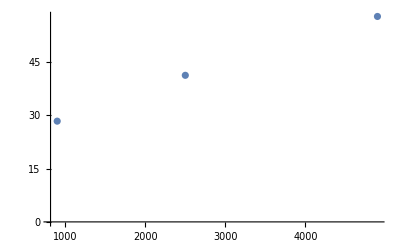

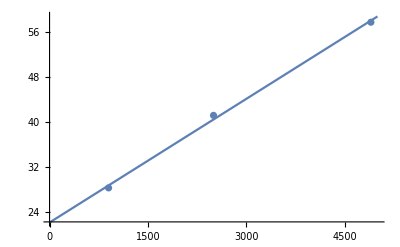

{{900,155.36},{2500,156.363},{}}

```mathematica
datforAC = {{30^2, 28.325},{50^2,41.2148},{70^2,57.7637}};
ListPlot[datforAC]
fitAC1 = FindFit[datforAC, off + s x, {off,s},x];
Show[Plot[fitAC1[[1,2]]+fitAC1[[2,2]]x,{x,15,5000},PlotRange->All],ListPlot[datforAC]]
datforAC2 = {{30^2, 155.36},{50^2,156.363},{}}
```

```mathematica
fitAC1;
```

{off→17.404,s→22160.9}

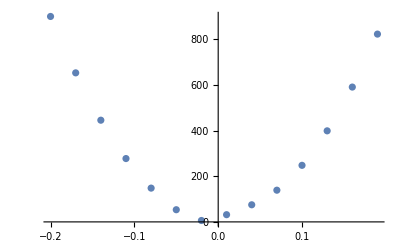

```mathematica
magdata = Table[i,{i,Bsolmin,Bsolmax,deltaBsol}];
fits = Flatten[Table[FindFit[finaldata[[i]], fitfunc[x],{ {offset,0.81}, {Amp,0.2},{Γ,0.6},{x1,1}}, x, MaxIterations->Infinity], {i,1,Length[finaldata]}]];
fits;
linecenters = Table[10^3fits[[4i,2]], {i,1, Length[fits]/4,1}];
plotdata = Table[{magdata[[i]],linecenters[[i]]},{i,1,Length[magdata]}];
ListPlot[plotdata, Axes-> False];
fit = FindFit[plotdata, off + s x^2, {off,s},x]
Show[ListPlot[plotdata]]
```

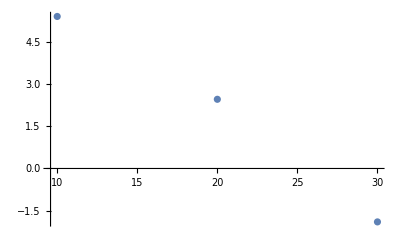

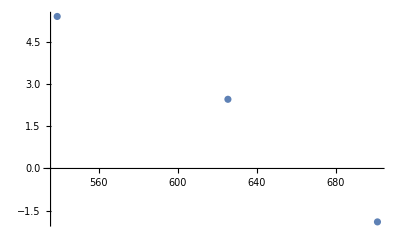

```mathematica
ACdata = Table[i,{i,mVmin,mVmax,mVdelta}];
fits2 = Flatten[Table[FindFit[finaldata[[i]], {fitfunc[x],Γ>0},{ {offset,0.05}, {Amp,0.3},{Γ,0.55},{x1,0.01}}, x, MaxIterations->Infinity], {i,1,Length[finaldata]}]];
fits2;
linecenters = Table[10^3fits2[[4i,2]], {i,1, Length[fits2]/4,1}];
widths = Table[2.74 10^3 fits2[[4i+3,2]],{i,0,Length[fits2]/4-1,1}];
plotdataAC = Table[{ACdata[[i]],linecenters[[i]]},{i,1,Length[ACdata]}];
plotdatawidths = Table[{widths[[i]],linecenters[[i]]},{i,1,Length[ACdata]}];
ListPlot[{plotdataAC }]
ListPlot[plotdatawidths,PlotRange-> All]
```

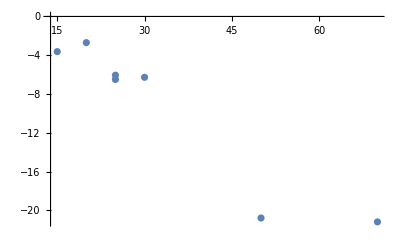

```mathematica
data5k = {{15,45.87-49.5},{25,43-49.5},{25,43.44-49.5},{20,46.8-49.5},{70,28.3-49.5},{30,43.22-49.5},{50,28.7-49.5}};
ListPlot[{data5k},PlotRange->All]
```

```mathematica
Bx2 = 2 10^-3
deltavtest = 10;
vmin = 100;
vmax = 1000;
Bsolt = 0.005;
min2 = -32Pi;
max2 =32Pi;
delta2 = 1;
normfact2 = Sum[F[vmin+deltavtest i],{i,0,(vmax-vmin)/deltavtest,1}]; 
Difftest = 
ParallelTable[
Diffs = NDSolve[{
c1'[t] == - ⅈ (σ2[0,Bsolt]c1[t] +Ω3[Bx2,t,v]c3[t]),
c2'[t] == - ⅈ (-σ2[0,Bsolt]c2[t]+Ω3[Bx2,t,v] c3[t]),
c3'[t]==- ⅈ (Ω3[Bx2,t,v]c1[t]+Ω3[Bx2,t,v]c2[t]+(Ω[B,t,v]/2 ) c4[t]),
c4'[t]==- ⅈ ((Ω[B,t,v]/2 )c3[t]-δ[Δ,Bsolt] c4[t]),
c1[0] ==0, c2[0]==0,c3[0] == 0, c4[0]==1}, {c1,c2,c3,c4}, {t,0,1.2 0.4/v}]; 
c1a[t_] = c1[t] /.Diffs[[1]];
c2a[t_] = c2[t] /. Diffs[[1]];
c3a[t_] = c3[t] /. Diffs[[1]];
c4a[t_] = c4[t] /. Diffs[[1]];
Abs[c1a[1.2 0.4/v]]^2+Abs[c2a[1.2 0.4/v]]^2+Abs[c3a[1.2 0.4/v]]^2,{v, vmin, vmax, deltavtest},{Δ, min2,max2,delta2}];
```

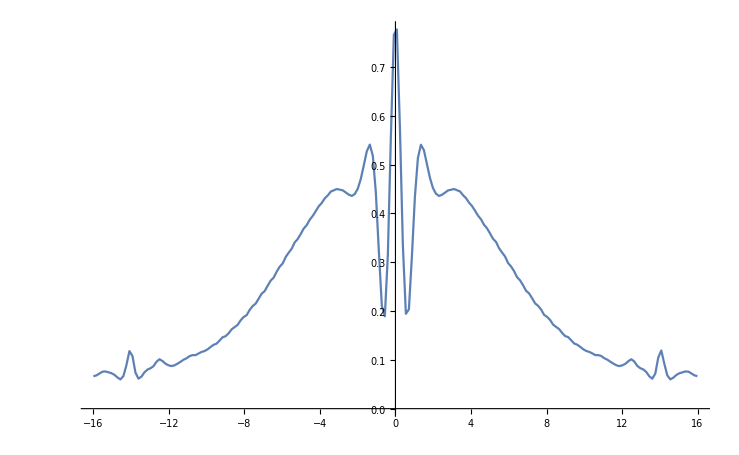

```mathematica
weightedtest = ParallelTable[F[vmin+deltavtest i-deltavtest]Difftest[[i]],{i,1,Length[Difftest],1}];
normtest =Length[weightedtest] Mean[weightedtest]/normfact2;
plotvar2 = ParallelTable[i/(2Pi), {i, min2,max2,delta2}];
finaldat = ParallelTable[{plotvar2[[i]], normtest[[i]]}, {i, 1, Length[plotvar2]}];
ListLinePlot[finaldat, PlotRange->All]
```

```mathematica
Diffsolvem1 = 
ParallelTable[
Diffs = NDSolve[{
c1'[t] == - ⅈ (σ2[Bsol]c1[t] +(Ωx[Bx,t,v]-ⅈ Ωy[By,t,v])c3[t]),
c2'[t] == - ⅈ (-σ2[Bsol]c2[t]+(Ωx[Bx,t,v]+ⅈ Ωy[By,t,v]) c3[t]),
c3'[t]==- ⅈ (Ωx[Bx,t,v](c1[t]+c2[t])+ⅈ Ωy[By,t,v](c1[t]-c2[t])+(Ω[B[[1,1,2]],t,v]/2 ) c4[t]),
c4'[t]==- ⅈ ((Ω[B[[1,1,2]],t,v]/2 )c3[t]-δ[Δ,Bsoltest,v] c4[t]),
c1[0] ==0, c2[0]==0,c3[0] == 0, c4[0]==1}, {c1,c2,c3,c4}, {t,0,1.2 0.4/v}]; 
c1a[t_] = c1[t] /.Diffs[[1]];
c2a[t_] = c2[t] /. Diffs[[1]];
c3a[t_] = c3[t] /. Diffs[[1]];
c4a[t_] = c4[t] /. Diffs[[1]];
Abs[c2a[1.2 0.4/v]]^2,{Bsol,Bsolmin,Bsolmax,deltaBsol},{v, velmin, velmax, deltav},{Δ, min,max,delta}];
weightedm1 = ParallelTable[F[velmin+deltav i-deltav]Diffsolvem1[[j,i]],{j,1,Length[Diffsolvem1],1},{i,1,Length[Diffsolvem1[[1]]],1}];
meanweightedm1 =ParallelTable[Sum[weightedm1[[i,j]],{j, 1, Length[weightedm1[[1]]]}], {i, 1, Length[weightedm1]}]/normfact;
plotvarm1 = Table[i/(2 Pi), {i,min,max,delta}];
finaldatam1=Table[{plotvarm1[[j]],meanweightedm1[[i,j]]}, {i,1,Length[Diffsolvem1],1}, {j,1, Length[meanweightedm1[[1]]]}];
```

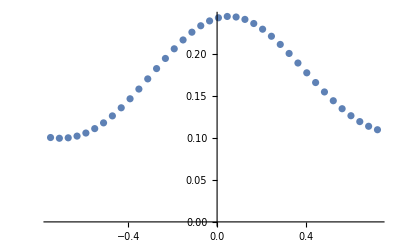

```mathematica
ListPlot[finaldatam1]
```

```mathematica
100/177 400/(4(0.3))/(2Pi)
```

29.9727

```mathematica
1/Sqrt[1/0.7^2+1/0.8^2+1/0.9^2+1/0.7^2]
```

0.381282